```mathematica
Remove["Global`*"]
```

# Logistic Map

### Governing equation:

```mathematica
f[r_, x_] := r x (1-x)
```

```mathematica
sol1 = Solve[f[r,x]==x,x]
```

{{x→0},{x→(-1+r)/r}}

```mathematica
sol2 = Solve[f[r,f[r,x]]==x,x]
```

{{x→0},{x→(-1+r)/r},{x→(r+r^2-r √(-3-2 r+r^2))/(2 r^2)},{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}}

```mathematica
sol3 = Solve[f[r,f[r, f[r,f[r,x]]]]==x,x];
```

```mathematica
f[x_Real,mu_Real,n_Real]:=Block[{y=x},Do[y=mu y (1-y),n];y]
mu[0]:=mu/.FindRoot[f[1,mu,2^0]==1,{mu,0.9}]
mu[1]:=mu/.FindRoot[f[1,mu,2^1]==1,{mu,0.9}]
mu[2]:=mu/.FindRoot[f[1,mu,2^2]==1/2,{mu,0.9}]
delta[n_]:=(mu[n-1]-mu[n-2])/(mu[n]-mu[n-1])
mu[n_]:=mu[n]=Module[{mu1=mu[n-1]+(mu[n-1]-mu[n-2])/delta[n-1],mu2=mu[n-1]+(mu[n-1]-mu[n-2])/(delta[n-1]+.01)},mu/.FindRoot[f[1,mu,2^n]==1,{mu,mu1,mu2},AccuracyGoal->10]]
Table[mu[n],{n,0,7}]
Table[delta[n],{n,2,7}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {mu} = {0.9}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

{0.9,0.9,0.9,0.88866,0.891667,0.892311,0.892449,0.892478}

FindRoot::jsing: Encountered a singular Jacobian at the point {mu} = {0.9}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.,-3.77159,4.6684,4.66895,4.66916}

```mathematica
Simplify[(D[f[r,x],x]/.sol2[[3]])*(D[f[r,x],x]/.sol2[[4]])]
```

4+2 r-r^2

```mathematica
Reduce[Abs[Simplify[(D[f[r,x],x]/.sol2[[3]]) (D[f[r,x],x]/.sol2[[4]])]]<1,{r}][[2,1]]
```

3<Re[r]<1+√6

```mathematica
D[f[r,f[r,x/.sol2[[3]]]],x]
```

0

```mathematica
f[r,x/.sol2[[3]]]
```

((r+r^2-r √(-3-2 r+r^2)) (1-(r+r^2-r √(-3-2 r+r^2))/(2 r^2)))/(2 r)

### Time series of the iterate values

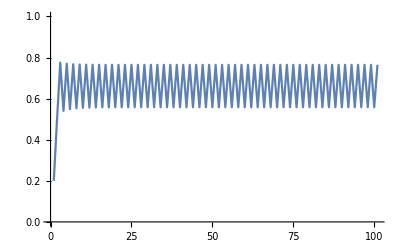

```mathematica
x0 = 0.2;
itr ={x0};
Do[
AppendTo[itr,f[3.1, itr[[-1]]]], {100}]
ListLinePlot[itr, PlotRange->{0,1}]
```

### Return Map:

```mathematica
Manipulate[Plot[{f[r, x],x}, {x, 0, 1}, PlotRange->{0,1}], {r, 0,4}]
```

```mathematica
Manipulate[Plot[{f[r,f[r,f[r, x]]],x}, {x, 0, 1}, PlotRange->{0,1}], {r, 3,4}]
```

### f(f(x))

```mathematica
Manipulate[Plot[{f[r,f[r, x]],x}, {x, 0, 1}, PlotRange->{0,1}], {r, 0,4}]
```

```mathematica
Manipulate[Plot[{f[r,f[r,f[r,f[r, x]]]],x}, {x, 0, 1}, PlotRange->{0,1}], {r, 0,4}]
```

```mathematica
sol = NSolve[1-k == (1-k^2)/(1-k^2(1-k))^2, k]
```

{{k→0.978734-1.12212 ⅈ},{k→0.978734+1.12212 ⅈ},{k→1.30445},{k→1.},{k→-0.859717},{k→-0.402197},{k→0.}}

```mathematica
α1 = 1/(k/.sol[[5]])
```

-1.16317

```mathematica
α2 = 1/(k/.sol[[6]])
```

-2.48634